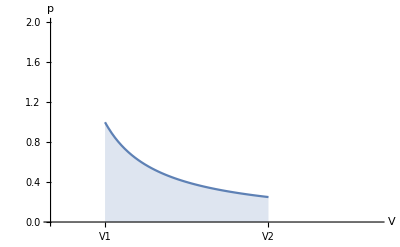

```mathematica
Plot[1/x,{x,1,4},PlotRange->{{0,6},{0,2}},Filling->Axis,AxesStyle->Thick,LabelStyle->Directive[Black,18],AxesLabel->{V,p},Ticks->{{{1,V1},{4,V2}}, None}]
```

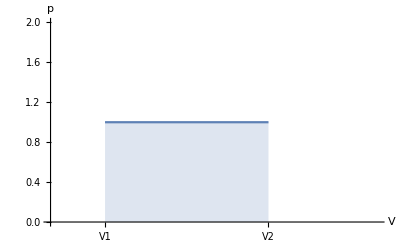

```mathematica
Plot[1,{x,1,4},PlotRange->{{0,6},{0,2}},Filling->Axis,AxesStyle->Thick,LabelStyle->Directive[Black,18],AxesLabel->{V,p},Ticks->{{{1,V1},{4,V2}}, None}]
```

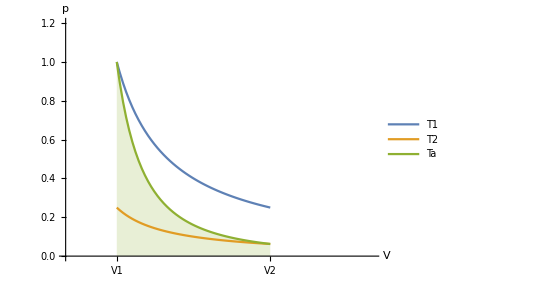

```mathematica
T1=1/x;
T2=1/(4x);
Ta=1/x^2;
Plot[{T1,T2,Ta},{x,1,4},PlotRange->{{0,6},{0,1.2}},AxesStyle->Thick,LabelStyle->Directive[Black,18],AxesLabel->{V,p},Ticks->{{{1,V1},{4,V2}}, None},Filling->{3->Axis},PlotLegends->"Expressions",AspectRatio->1/1.4]
```

```mathematica
Table[Graphics[Rotate[Circle[{6,6},{4,2}],Pi/7],LabelStyle->Directive[Black,18],Axes->True,Ticks-> None,AxesLabel->{V,p},AxesStyle->Thick,PlotRange->{{0,12},{0,10}}],{n,4}]
```